```mathematica
a={3,3,-4,1};
b={5,3,-4,1};
c={5,5,-4,1};
d={3,5,-4,1};
aPrime={3,3,-6,1};
bPrime={5,3,-6,1};
cPrime={5,5,-6,1};
dPrime={3,5,-6,1};
d2Prime={8,8,-6,1};
Wxmin= {2,3,1};
Wxmax= {5,3,1};
Hymin= {3,2,1};
Hymax= {3,5,1};
WorldPoints = {a,b,c,d,aPrime,bPrime,cPrime,dPrime,d2Prime};
Oc={0,0,0,1};
zeta1 = -1;
zeta2=-1;
alpha=25;
beta = 0;
Oc2={6,0,0,1};
Rot2=RotationsE2[alpha];
Rot1=RotationsE2[beta];
ObjectSize = b[[1]]-a[[1]];
A={{1,0,0,0},{0,1,0,0},{0,0,1,0},{0,0,0,1}};
AK={{1,0,0},{0,1,0},{0,0,1}};
```

```mathematica
ClearAll["Global`*"];
```

PM1 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

PM2 = {{-1,0,0,0},{0,-1,0,0},{0,0,-1,0},{0,0,1,0}}

OC2 = {6,0,0,1}

M of C2=(1 | 0 | 0 | 0
0 | 1 | 0 | 0
0 | 0 | 1 | 0
0 | 0 | 0 | 1)

M2 of C1 =(0.906308 | 0. | -0.422618 | -5.43785
0. | 1. | 0. | 0.
0.422618 | 0. | 0.906308 | -2.53571
0. | 0. | 0. | 1.)

ProjectionMtxCamera1(-1 | 0 | 0 | 0
0 | -1 | 0 | 0
0 | 0 | -1 | 0
0 | 0 | 1 | 0)

ProjectionMtxCamera2(-0.906308 | 0. | 0.422618 | 5.43785
0. | -1. | 0. | 0.
-0.422618 | 0. | -0.906308 | 2.53571
0.422618 | 0. | 0.906308 | -2.53571)

CameraProjectedPointsK1 = (-3 | -3 | 4 | -4
-5 | -3 | 4 | -4
-5 | -5 | 4 | -4
-3 | -5 | 4 | -4
-3 | -3 | 6 | -6
-5 | -3 | 6 | -6
-5 | -5 | 6 | -6
-3 | -5 | 6 | -6
-8 | -8 | 6 | -6)

CameraProjectedPointsK2 = (1.02845 | -3. | 4.89309 | -4.89309
-0.784165 | -3. | 4.04785 | -4.04785
-0.784165 | -5. | 4.04785 | -4.04785
1.02845 | -5. | 4.89309 | -4.89309
0.183214 | -3. | 6.7057 | -6.7057
-1.6294 | -3. | 5.86046 | -5.86046
-1.6294 | -5. | 5.86046 | -5.86046
0.183214 | -5. | 6.7057 | -6.7057
-4.34833 | -8. | 4.59261 | -4.59261)

homogene CameraProjectedPointsK1 = (3/4 | 3/4 | -1 | 1
5/4 | 3/4 | -1 | 1
5/4 | 5/4 | -1 | 1
3/4 | 5/4 | -1 | 1
1/2 | 1/2 | -1 | 1
5/6 | 1/2 | -1 | 1
5/6 | 5/6 | -1 | 1
1/2 | 5/6 | -1 | 1
4/3 | 4/3 | -1 | 1)

homogene CameraProjectedPointsK2 = (-0.210184 | 0.61311 | -1. | 1.
0.193724 | 0.741134 | -1. | 1.
0.193724 | 1.23522 | -1. | 1.
-0.210184 | 1.02185 | -1. | 1.
-0.0273221 | 0.44738 | -1. | 1.
0.278033 | 0.511905 | -1. | 1.
0.278033 | 0.853175 | -1. | 1.
-0.0273221 | 0.745634 | -1. | 1.
0.946809 | 1.74193 | -1. | 1.)

Begin construct Epipol_______________________________________________

End construct Epipol_______________________________________________

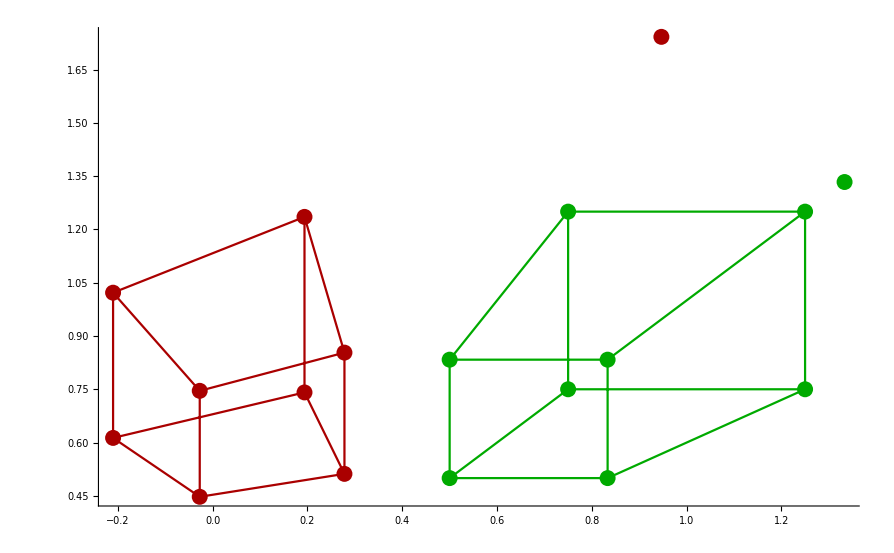

ImagePlaneC1Points = (3/4 | 3/4 | 1
5/4 | 3/4 | 1
5/4 | 5/4 | 1
3/4 | 5/4 | 1
1/2 | 1/2 | 1
5/6 | 1/2 | 1
5/6 | 5/6 | 1
1/2 | 5/6 | 1
4/3 | 4/3 | 1)

ImagePlaneC2Points = (-0.210184 | 0.61311 | 1.
0.193724 | 0.741134 | 1.
0.193724 | 1.23522 | 1.
-0.210184 | 1.02185 | 1.
-0.0273221 | 0.44738 | 1.
0.278033 | 0.511905 | 1.
0.278033 | 0.853175 | 1.
-0.0273221 | 0.745634 | 1.
0.946809 | 1.74193 | 1.)

CoefficientMtx = (-0.157638 | -0.157638 | -0.210184 | 0.459833 | 0.459833 | 0.61311 | 0.75 | 0.75 | 1.
0.242155 | 0.145293 | 0.193724 | 0.926418 | 0.555851 | 0.741134 | 1.25 | 0.75 | 1.
0.242155 | 0.242155 | 0.193724 | 1.54403 | 1.54403 | 1.23522 | 1.25 | 1.25 | 1.
-0.157638 | -0.26273 | -0.210184 | 0.766388 | 1.27731 | 1.02185 | 0.75 | 1.25 | 1.
-0.013661 | -0.013661 | -0.0273221 | 0.22369 | 0.22369 | 0.44738 | 0.5 | 0.5 | 1.
0.231694 | 0.139016 | 0.278033 | 0.426587 | 0.255952 | 0.511905 | 0.833333 | 0.5 | 1.
0.231694 | 0.231694 | 0.278033 | 0.710979 | 0.710979 | 0.853175 | 0.833333 | 0.833333 | 1.
-0.013661 | -0.0227684 | -0.0273221 | 0.372817 | 0.621362 | 0.745634 | 0.5 | 0.833333 | 1.
1.26241 | 1.26241 | 0.946809 | 2.32257 | 2.32257 | 1.74193 | 1.33333 | 1.33333 | 1.)

MatrixRank[CoefficientMtx]8

ns ={{2.05699×10^-15,-0.298836,8.37199×10^-16,3.19564×10^-15,-2.57523×10^-15,0.707107,-2.48879×10^-15,-0.640856,2.07478×10^-16}}

F = (2.05699×10^-15 | -0.298836 | 8.37199×10^-16
3.19564×10^-15 | -2.57523×10^-15 | 0.707107
-2.48879×10^-15 | -0.640856 | 2.07478×10^-16)

lC1 = {{-0.224127,0.707107,-0.480642},{-0.224127,0.707107,-0.480642},{-0.373545,0.707107,-0.80107},{-0.373545,0.707107,-0.80107},{-0.149418,0.707107,-0.320428},{-0.149418,0.707107,-0.320428},{-0.24903,0.707107,-0.534047},{-0.24903,0.707107,-0.534047},{-0.398448,0.707107,-0.854475}}

lPrimeC1 = {{-9.61857×10^-16,-0.578046,0.433534},{2.78099×10^-16,-0.698748,0.524061},{1.85703×10^-15,-0.698748,0.873435},{3.4433×10^-16,-0.578046,0.722557},{-1.11532×10^-15,-0.632692,0.316346},{-2.81013×10^-16,-0.723943,0.361971},{8.09563×10^-16,-0.723943,0.603286},{-1.62211×10^-16,-0.632692,0.527243},{5.02537×10^-15,-0.923797,1.23173}}

e = {-1.,1.9984×10^-15,4.56533×10^-15}

e' = {0.906308,-2.57315×10^-15,-0.422618}

EpipoleLines = (0.466308 | -1.47117 | 1.
0.466308 | -1.47117 | 1.
0.466308 | -0.882702 | 1.
0.466308 | -0.882702 | 1.
0.466308 | -2.20676 | 1.
0.466308 | -2.20676 | 1.
0.466308 | -1.32405 | 1.
0.466308 | -1.32405 | 1.
0.466308 | -0.827533 | 1.)

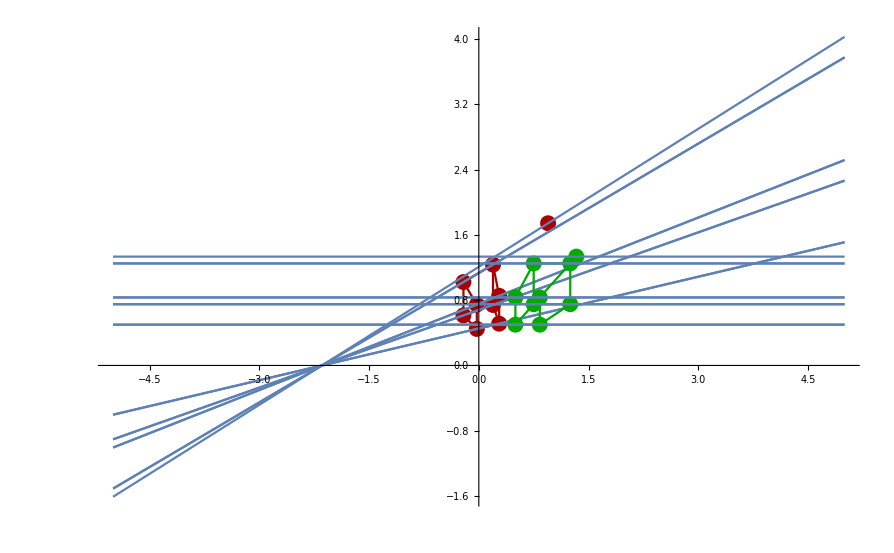

Begin Computing essential Matrix___________________________________________________

EMtx = (2.05699×10^-15 | -0.298836 | -8.37199×10^-16
3.19564×10^-15 | -2.57523×10^-15 | -0.707107
2.48879×10^-15 | 0.640856 | 2.07478×10^-16)

U of E = {{0.,-0.422618,-0.906308},{-1.,-1.99881×10^-15,9.48971×10^-16},{-2.22045×10^-15,0.906308,-0.422618}}

Sigma of E = {{0.707107,0.,0.},{0.,0.707107,0.},{0.,0.,0.}}

V of E = {{-4.54406×10^-15,1.88738×10^-15,-1.},{-2.80153×10^-15,1.,1.9984×10^-15},{1.,2.80153×10^-15,-4.56533×10^-15}}

S1 = (0. | 0.422618 | 9.38401×10^-16
-0.422618 | 0. | 0.906308
-9.38401×10^-16 | -0.906308 | 0.)

S2 = (0. | -0.422618 | -9.38401×10^-16
0.422618 | 0. | -0.906308
9.38401×10^-16 | 0.906308 | 0.)

R1 = (0.906308 | -2.99514×10^-15 | 0.422618
-2.83635×10^-15 | -1. | -8.02718×10^-16
0.422618 | -5.25959×10^-16 | -0.906308)

R2 = (0.906308 | -6.27189×10^-16 | -0.422618
9.38408×10^-16 | 1. | 8.02718×10^-16
0.422618 | -1.16316×10^-15 | 0.906308)

Test R1 is rotation ={{1.,-1.00453×10^-16,5.55112×10^-17},{-1.00453×10^-16,1.,1.35955×10^-17},{5.55112×10^-17,1.35955×10^-17,1.}}

Test R2 is rotation ={{1.,-1.21592×10^-16,5.55112×10^-17},{-1.21592×10^-16,1.,1.35955×10^-17},{5.55112×10^-17,1.35955×10^-17,1.}}

Check if t of S1, S2 is equal = {{{0.906308,-8.77776×10^-16,0.422618}},{{-0.906308,7.87558×10^-16,-0.422618}}}

t = {0.906308,-8.77776×10^-16,0.422618}

P21  = (0.906308 | -6.27189×10^-16 | -0.422618 | -0.906308
9.38408×10^-16 | 1. | 8.02718×10^-16 | 8.77776×10^-16
0.422618 | -1.16316×10^-15 | 0.906308 | -0.422618)

P22  = (0.906308 | -2.99514×10^-15 | 0.422618 | -0.906308
-2.83635×10^-15 | -1. | -8.02718×10^-16 | 8.77776×10^-16
0.422618 | -5.25959×10^-16 | -0.906308 | -0.422618)

P23  = (0.906308 | -6.27189×10^-16 | -0.422618 | 0.906308
9.38408×10^-16 | 1. | 8.02718×10^-16 | -8.77776×10^-16
0.422618 | -1.16316×10^-15 | 0.906308 | 0.422618)

P24  = (0.906308 | -2.99514×10^-15 | 0.422618 | 0.906308
-2.83635×10^-15 | -1. | -8.02718×10^-16 | -8.77776×10^-16
0.422618 | -5.25959×10^-16 | -0.906308 | 0.422618)

End Computing essential Matrix___________________________________________________

PList = {{{0.906308,-6.27189×10^-16,-0.422618,-0.906308},{9.38408×10^-16,1.,8.02718×10^-16,8.77776×10^-16},{0.422618,-1.16316×10^-15,0.906308,-0.422618}},{{0.906308,-2.99514×10^-15,0.422618,-0.906308},{-2.83635×10^-15,-1.,-8.02718×10^-16,8.77776×10^-16},{0.422618,-5.25959×10^-16,-0.906308,-0.422618}},{{0.906308,-6.27189×10^-16,-0.422618,0.906308},{9.38408×10^-16,1.,8.02718×10^-16,-8.77776×10^-16},{0.422618,-1.16316×10^-15,0.906308,0.422618}},{{0.906308,-2.99514×10^-15,0.422618,0.906308},{-2.83635×10^-15,-1.,-8.02718×10^-16,-8.77776×10^-16},{0.422618,-5.25959×10^-16,-0.906308,0.422618}}}

Length PList = 4

End Reconstruction of Rotation and Translation________________________________________________

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{0.5,0.5,-0.666667},{0.833333,0.5,-0.666667},{0.833333,0.833333,-0.666667},{0.5,0.833333,-0.666667},{0.5,0.5,-1.},{0.833333,0.5,-1.},{0.833333,0.833333,-1.},{0.5,0.833333,-1.},{1.33333,1.33333,-1.}}

ScaleValue = 6.

RForOk2 = {{0.906308,9.38408×10^-16,0.422618},{-6.27189×10^-16,1.,-1.16316×10^-15},{-0.422618,8.02718×10^-16,0.906308}}

tForOK2 = {-0.906308,8.77776×10^-16,-0.422618}

t = {1.,-1.93778×10^-15,4.66294×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
5. | 3. | -4.
5. | 5. | -4.
3. | 5. | -4.
3. | 3. | -6.
5. | 3. | -6.
5. | 5. | -6.
3. | 5. | -6.
8. | 8. | -6.)

-Graphics3D-

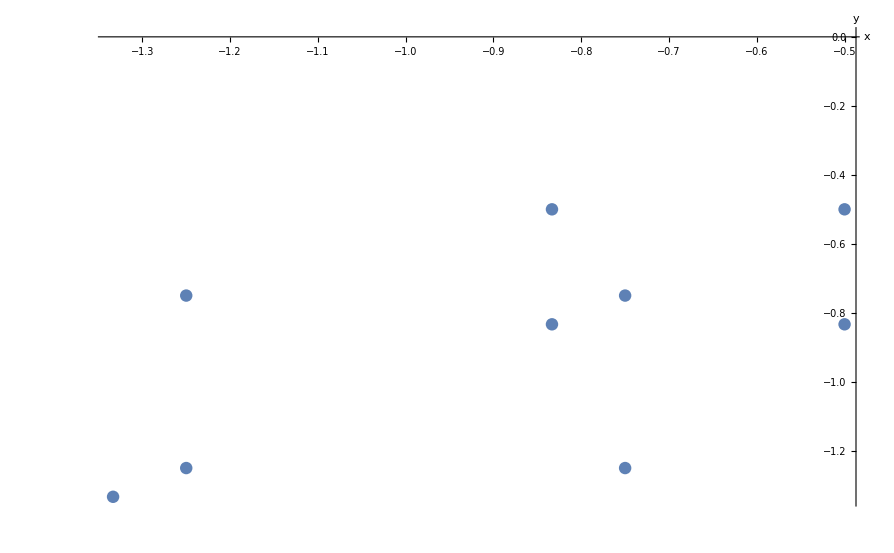

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-4.37024×10^13,-4.37024×10^13,5.82699×10^13},{1.25,0.75,-1.},{1.25,1.25,-1.},{-4.46421×10^13,-7.44035×10^13,5.95228×10^13},{-3.66126×10^13,-3.66126×10^13,7.32252×10^13},{1.25,0.75,-1.5},{1.25,1.25,-1.5},{-3.52634×10^13,-5.87723×10^13,7.05267×10^13},{0.8,0.8,-0.6}}

ScaleValue = -6.86461×10^-14

RForOk2 = {{0.906308,-2.83635×10^-15,0.422618},{-2.99514×10^-15,-1.,-5.25959×10^-16},{0.422618,-8.02718×10^-16,-0.906308}}

tForOK2 = {-0.906308,8.77776×10^-16,-0.422618}

t = {1.,-2.05903×10^-15,4.4964×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
-8.58076×10^-14 | -5.14846×10^-14 | 6.86461×10^-14
-8.58076×10^-14 | -8.58076×10^-14 | 6.86461×10^-14
3.06451 | 5.10751 | -4.08601
2.51331 | 2.51331 | -5.02662
-8.58076×10^-14 | -5.14846×10^-14 | 1.02969×10^-13
-8.58076×10^-14 | -8.58076×10^-14 | 1.02969×10^-13
2.42069 | 4.03449 | -4.84138
-5.49169×10^-14 | -5.49169×10^-14 | 4.11877×10^-14)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{-0.5,-0.5,0.666667},{-0.833333,-0.5,0.666667},{-0.833333,-0.833333,0.666667},{-0.5,-0.833333,0.666667},{-0.5,-0.5,1.},{-0.833333,-0.5,1.},{-0.833333,-0.833333,1.},{-0.5,-0.833333,1.},{-1.33333,-1.33333,1.}}

ScaleValue = -6.

RForOk2 = {{0.906308,9.38408×10^-16,0.422618},{-6.27189×10^-16,1.,-1.16316×10^-15},{-0.422618,8.02718×10^-16,0.906308}}

tForOK2 = {0.906308,-8.77776×10^-16,0.422618}

t = {-1.,1.93778×10^-15,-4.66294×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
5. | 3. | -4.
5. | 5. | -4.
3. | 5. | -4.
3. | 3. | -6.
5. | 3. | -6.
5. | 5. | -6.
3. | 5. | -6.
8. | 8. | -6.)

-Graphics3D-

-Graphics-

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

K1,K2 =  (-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)(-1 | 0 | 0
0 | -1 | 0
0 | 0 | 1)

«6 more identical outputs»

-Graphics3D-

Reconstructed Points 3D = {{4.37024×10^13,4.37024×10^13,-5.82699×10^13},{-1.25,-0.75,1.},{-1.25,-1.25,1.},{4.46421×10^13,7.44035×10^13,-5.95228×10^13},{3.66126×10^13,3.66126×10^13,-7.32252×10^13},{-1.25,-0.75,1.5},{-1.25,-1.25,1.5},{3.52634×10^13,5.87723×10^13,-7.05267×10^13},{-0.8,-0.8,0.6}}

ScaleValue = 6.86461×10^-14

RForOk2 = {{0.906308,-2.83635×10^-15,0.422618},{-2.99514×10^-15,-1.,-5.25959×10^-16},{0.422618,-8.02718×10^-16,-0.906308}}

tForOK2 = {0.906308,-8.77776×10^-16,0.422618}

t = {-1.,2.05903×10^-15,-4.4964×10^-15}

Reconstructed scaled Points 3D = (3. | 3. | -4.
-8.58076×10^-14 | -5.14846×10^-14 | 6.86461×10^-14
-8.58076×10^-14 | -8.58076×10^-14 | 6.86461×10^-14
3.06451 | 5.10751 | -4.08601
2.51331 | 2.51331 | -5.02662
-8.58076×10^-14 | -5.14846×10^-14 | 1.02969×10^-13
-8.58076×10^-14 | -8.58076×10^-14 | 1.02969×10^-13
2.42069 | 4.03449 | -4.84138
-5.49169×10^-14 | -5.49169×10^-14 | 4.11877×10^-14)

-Graphics3D-

-Graphics-

Begin New Rectification with Disortion minimization criterion_______________________________________________

pi = {{0.75,0.75,1.},{1.25,0.75,1.},{1.25,1.25,1.},{0.75,1.25,1.},{0.5,0.5,1.},{0.833333,0.5,1.},{0.833333,0.833333,1.},{0.5,0.833333,1.},{1.33333,1.33333,1.}}

pj = {{-0.210184,0.61311,1.},{0.193724,0.741134,1.},{0.193724,1.23522,1.},{-0.210184,1.02185,1.},{-0.0273221,0.44738,1.},{0.278033,0.511905,1.},{0.278033,0.853175,1.},{-0.0273221,0.745634,1.},{0.946809,1.74193,1.}}

n = 9

minXpi = 0.5

maxXPi = 1.33333

minYpi = 0.5

maxYPi = 1.33333

minXPj = -0.210184

maxXPj = 0.946809

minYPj = 0.44738

maxYPj = 1.74193

piWidth = 3.

piHeight = 3.

pjWidth = 3.

pjHeight = 3.

pc = (0.888889
0.888889
1.)

pcPrime = (0.157257
0.879038
1.)

P = {{-0.138889,0.361111,0.361111,-0.138889,-0.388889,-0.0555556,-0.0555556,-0.388889,0.444444},{-0.138889,-0.138889,0.361111,0.361111,-0.388889,-0.388889,-0.0555556,-0.0555556,0.444444},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

PPrime = {{-0.367441,0.0364673,0.0364673,-0.367441,-0.184579,0.120776,0.120776,-0.184579,0.789552},{-0.265928,-0.137904,0.356186,0.142812,-0.431657,-0.367133,-0.0258633,-0.133404,0.862891},{0.,0.,0.,0.,0.,0.,0.,0.,0.}}

PP = {{0.805556,0.444444,0.},{0.444444,0.805556,0.},{0.,0.,0.}}

PPPrime = {{0.993391,0.791329,0.},{0.791329,1.32116,0.},{0.,0.,0.}}

pc = {0.888889,0.888889,1.}

pcpc = {{0.790123,0.790123,0.888889},{0.790123,0.790123,0.888889},{0.888889,0.888889,1.}}

pcpcPrime = {{0.0247296,0.138235,0.157257},{0.138235,0.772708,0.879038},{0.157257,0.879038,1.}}

A = (1.67896×10^-29 | -9.26321×10^-30 | 3.67763×10^-15
-9.26321×10^-30 | 1.67896×10^-29 | -2.02903×10^-15
3.67763×10^-15 | -2.02903×10^-15 | 0.805556)

B = (4.75336×10^-30 | -1.97634×10^-15 | 1.37035×10^-15
-1.97634×10^-15 | 0.821722 | -0.569764
1.37035×10^-15 | -0.569764 | 0.395062)

APrime = (0.235967 | -0.141336 | 0.506034
-0.141336 | 0.177426 | -0.303097
0.506034 | -0.303097 | 1.08519)

BPrime = (2.08246×10^-31 | -3.45669×10^-16 | -2.43271×10^-16
-1.69113×10^-16 | 1.5571×10^-15 | -0.350155
5.38969×10^-31 | -0.486384 | 1.28963×10^-16)

{A[[1,1;;2]],A[[2,1;;2]]}={{1.67896×10^-29,-9.26321×10^-30},{-9.26321×10^-30,1.67896×10^-29}}

{APrime[[1,1;;2]],APrime[[2,1;;2]]}={{0.235967,-0.141336},{-0.141336,0.177426}}

DD ={{4.09751×10^-15,-2.26069×10^-15},{0.,3.41743×10^-15}}

DDPrime ={{0.485765,-0.290956},{0.,0.304582}}

{B[[1,1;;2]],B[[2,1;;2]]}={{4.75336×10^-30,-1.97634×10^-15},{-1.97634×10^-15,0.821722}}

{BPrime[[1,1;;2]],BPrime[[2,1;;2]]}={{2.08246×10^-31,-3.45669×10^-16},{-1.69113×10^-16,1.5571×10^-15}}

DTBD[[2,1]] = {-2.00594×10^-15,1.}

Eigensystem DTB1 = {{7.03599×10^28,-1.11022×10^-16},{{-2.00594×10^-15,1.},{-1.,-2.00594×10^-15}}}

Eigensystem DTBPrimeD = {{1.36564×10^-14,-1.95542×10^-16},{{0.168628,-0.98568},{-0.996516,-0.0834055}}}

z1 first = {1.61444×10^14,2.92618×10^14}

z1= {1.61444×10^14,2.92618×10^14}

z2 first = {-1.59122,-3.23617}

z2= {-1.59122,-3.23617}

z ={3.34199×10^14,3.34199×10^14,0.}

w = {-1.52573,1.52573,-3.34199×10^14}

wPrime = {-9.98709×10^13,0.207342,-2.14174×10^14}

wPrime = {0.466308,-9.68103×10^-16,1.}

w = {4.56533×10^-15,-4.56533×10^-15,1.}

HpPrime = (1. | 0. | 0.
0. | 1. | 0.
0.466308 | -9.68103×10^-16 | 1.)

Hp = (1. | 0. | 0.
0. | 1. | 0.
4.56533×10^-15 | -4.56533×10^-15 | 1.)

ePrime inf = {0.906308,-2.57315×10^-15,-8.32667×10^-15}

e inf = {-1.,1.9984×10^-15,0.}

HrPrime = (-0.707107 | 7.4045×10^-16 | 0.
-7.4045×10^-16 | -0.707107 | 1.
0. | 0. | 1.)

Hr = (-0.640856 | 2.48879×10^-15 | 0.
-2.48879×10^-15 | -0.640856 | 1.
0. | 0. | 1.)

ePrimeHorizontal = {-0.640856,-7.17826×10^-15,-8.32667×10^-15}

eHorizontal = {0.640856,1.2081×10^-15,0.}

piA = {1,0,1}

piB = {2,1,1}

piC = {1,2,1}

piD = {0,1,1}

piX = {2,0,0}

piY = {0,2,0}

piSA = -1.

piSB = 0.

pjA = {1.,0.,1.}

pjB = {2.,1.,1.}

pjC = {1.,2.,1.}

pjD = {0.,1.,1.}

pjX = {2.,0.,0.}

pjY = {0.,2.,0.}

pjSA = -1.

pjSB = 0.

RecPointsC1 =(0.480642 | 0.519358 | 1.
0.80107 | 0.519358 | 1.
0.80107 | 0.19893 | 1.
0.480642 | 0.19893 | 1.
0.320428 | 0.679572 | 1.
0.534047 | 0.679572 | 1.
0.534047 | 0.465953 | 1.
0.320428 | 0.465953 | 1.)

RecPointsC2 =(-0.164772 | 0.519358 | 1.
0.125634 | 0.519358 | 1.
0.125634 | 0.19893 | 1.
-0.164772 | 0.19893 | 1.
-0.019569 | 0.679572 | 1.
0.174035 | 0.679572 | 1.
0.174035 | 0.465953 | 1.
-0.019569 | 0.465953 | 1.)

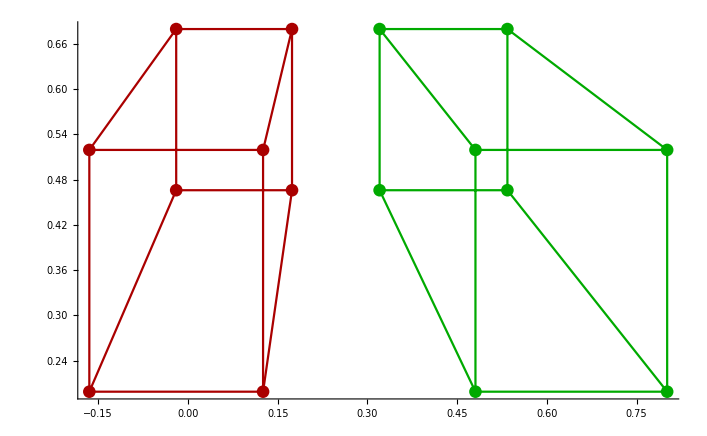

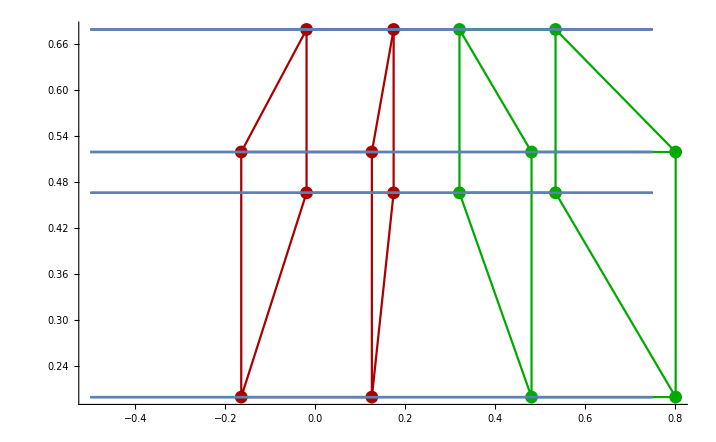

End New Rectification with Disortion minimization criterion_______________________________________________

```mathematica
StartComputation[];
```